((1+x)^2+(1+y)^4≤16&&(1+x)^2+(-1+y)^4≤16&&(-1+x)^2+(1+y)^4≤16&&(-1+x)^2+(-1+y)^4≤16)||((1+x)^4+(1+y)^2≤16&&(1+x)^4+(-1+y)^2≤16&&(-1+x)^4+(1+y)^2≤16&&(-1+x)^4+(-1+y)^2≤16)||(x^2≤3&&y^2≤3)

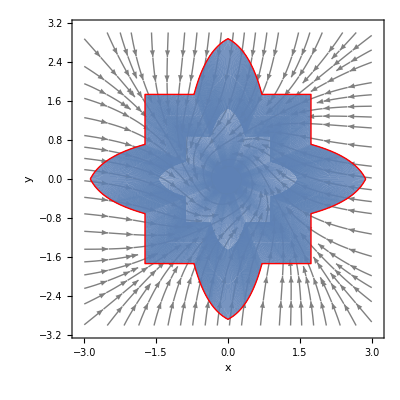

```mathematica
vf={-x^3-y, -y^3+x};
shape=And@@(Table[(x-x0)^2+(y-y0)^4≤16,{x0,-1,1,2},{y0,-1,1,2}]//Flatten) || And@@(Table[(x-x0)^4+(y-y0)^2≤16,{x0,-1,1,2},{y0,-1,1,2}]//Flatten) ||
(x^2≤3 &&y^2≤3)(* || And@@(Table[(x-x0)^2+(y-y0)^2≤9,{x0,-1,1,1},{y0,-1,1,1}]//Flatten)  *)
ℛ=ImplicitRegion[shape,{x,y}];

Show[
StreamPlot[vf,{x,-3,3},{y,-3,3},
 StreamStyle->Gray,
FrameLabel->{
Style[TraditionalForm[x],18, Black], 
Style[TraditionalForm[y],18, Black]},
LabelStyle->{FontFamily->"Source Serif Pro"},
 FrameTicks->Automatic,
 PlotRangePadding->0],
RegionPlot[BoundaryDiscretizeRegion[ℛ,MaxCellMeasure->{"Length"->0.02}], 
BoundaryStyle->{Thick, Red}
]
]
```

```mathematica
ES`ContinuousInvariantQ[shape,vf, {x,y}, True]//Timing
```

{7.92385,True}

```mathematica
LZZ`ContinuousInvariantQ[shape,vf, {x,y}, True]//Timing
```

{1852.,True}